# Introduction to Mathematica

“The computer is incredibly fast, accurate, and stupid. 
Man is incredibly slow, inaccurate, and brilliant. 
The marriage of the two is a force beyond calculation.”
-- Leo Cherne (probably)

Pen and paper mathematics can only get you so far. Much of modern biology is helped along by computers, and this is doubly true for mathematical modeling. They allow us to simulate populations of organisms and solve equations that, if we tried to do them by hand, would destroy our souls. 

The problem is that computers are stupid. Not just ordinary-stupid, but advanced-stupid. They are literally rocks that we tricked into thinking for us. They’re a long way from understanding human speech, or figuring out the intention behind what we ask them to do. To get the computer to do what we want we have to spell out exactly what we want in a programming language. Python, R, C++, Java, and Julia are all popular languages. For this class we choose to use the Wolfram language, which we can access in Mathematica, because it is particularly strong at manipulating equations, simple simulations, and making pretty pretty graphs.

(But it also crashes a bunch so make sure you save regularly.)

## Simulating a population.

## 1. Simple growth simulation (and intro to Mathematica-cells)

We’ll learn by doing and dive in with a simple bacteria simulation. Say that we have bacteria. Each generation 10% of the bacteria replicates, meaning the population size grows by 10% each generation. Say we start with 1618 bacteria (generation zero) and want to calculate how many bacteria are in the next generation. Then we can use Mathematica as an over-glorified calculator.

```mathematica
(* Put your cursor here and press Shift-Enter to calculate the answer.*)
1618*1.1
```

1779.8

We have around 1779.8 bacteria in the first generation. Notice that multiplication is denoted by the asterisk, but if you’re feeling lazy you can just put a space inbetween the two numbers.

```mathematica
1618 1.1
```

1779.8

The number of bacteria in the second generation will be the value of the first generation times 1.1.

```mathematica
1779.8 * 1.1  (* Generation 2 *)
```

1957.78

and the next one is

```mathematica
1957.78 * 1.1  (* Generation 3 *)
```

2153.56

Right now this is just a fancy calculator with code sections and text sections. These sections are called cells, which are indicated by the grey square brackets on the very right. Some cells, like this one, are text cells. Others, like the one above, are code cells. If you place your cursor in a code cell and press Shift-Enter Mathematica will execute the code there  You can also use the numpad’s Enter for this. Try changing one of the above code cells and executing it.

To make your own cell move your cursor below a cell until the cursor turns horizontal. Click and you’ll create a new code cell. Try it and calculate the next generation’s population size below. You should get 2368.92.

Other ways to make a cell are 

	1. Press the down (or up) arrow until the cursor turns horizontal, then start typing. This will create a code cell.
	2. Press Alt-Enter. This will create a cell below of the same type.
	
You can change a cell’s type (also called style) through the following hotkeys.

-Graphics-
Try creating a text cell below and writing a beautiful haiku about your love of biology.

You can delete cells by selecting the cell brackets and pressing delete. Try deleting this cell .

You can collapse and open cells by double clicking the square brackets. The bracket with the little arrow is one you can open. Open the section below.

#### Open this section by double clicking the square bracket on the right.

Now let’s continue on with our calculations. We were at 2368.92 bacteria at generation four. What is it at generation ten? To find this we could continue copy-pasting numbers as we have been doing...

```mathematica
2368.92 * 1.1 (* Generation 5 *)
```

2605.81

```mathematica
2605.81 * 1.1 (* Generation 6 *)
```

2866.39

```mathematica
2866.39 * 1.1 (* Generation 7 *)
```

3153.03

Copying each number and multiplying it by 1.1 is a drag. If we wanted to calculate to generation 100 then it would be more than a drag. One might say that this copy-past strategy is (to use the technical term) small brained. 

-Graphics-

In the next section we show a slightly better way to do this using a Slick Trick^TM.

#### Previous values

The % symbol to give the last calculated value. Re-run the generation 5 cell in the pervious section then run this next cell.

```mathematica
% * 1.1
```

4196.68

The % symbol is replaced by whatever the last calculated cell was. This means we can keep bashing Shift-Enter we take the previous population size and increase it by ten percent. This trick allows us to easily reach ten generations.

Now’s a good time to mention that the order you run the cells in matters. Try re-running the generation 5 cell then running the % * 1.1 cell. You’ll see that takes % to equal 2605.81 because that was the last cell run. 

This means the order that cells are placed in your notebook doesn’t matter, but the order that you execute them in does matter. You can move freely around your notebook to execute cells, but you need to remember what you have already done. This does not just go for the % symbol, but everything in Mathematica. Many a bug has appeared from running things in the wrong order.

The % trick is fine, but say you wanted to go back and see what the population size was in generation 8. We can’t because that data is lost to us. Mathematica ran the code and promptly forgot about the output. To save outputs we’ll need variables.

## 2. Variables

Think of variables as name-tags you attach to data. This gives you an easy way to find them later. Let’s say we just calculated the size of generation 10 to be 4196.68 and are so pleased by this number that we wish to save it.  The “=” sign is the tool we need.

```mathematica
gen10 = 4196.68
```

4196.68

Notice that when you run the above cell gen10 goes from a blue font to a black font. A variable with black font has a value, where one with a blue font has no value and is treated as a symbol. We can access the value of gen10 simply by writing gen10 in the code.

```mathematica
gen10
```

4196.68

We can multiply gen10, run code on it, or anything. With a value assigned to gen10 Mathematica now treats it as a number.

```mathematica
gen10 + 10000
gen10-10000
gen10 * 2
gen10 /2
```

14196.7

-5803.32

8393.36

2098.34

Notice Mathematica outputs every line. We can suppress this adding a semicolon at the end of a line. This tells Mathematica to do the calculation but not print the output, which helps control clutter.

```mathematica
gen11 = gen10 * 1.1;
gen12 = gen11 * 1.1
```

5077.98

We only get the data for the second line, but the calculations (including variable assignments) are done for both lines. See that we can access gen11’s value.

```mathematica
gen11
```

4616.35

Variables are nice because we can use previous values in calculations.

```mathematica
avg = (gen11 + gen12)/2 (* Average of last two generations. Ctrl+/ let's you write the fraction *)
```

4847.17

We can also update variables to new values with a new assignment. They are not constant and set in stone once you assign them. Instead they are fluid and, you might say, variable.

```mathematica
avg = -999;
avg
```

-999

One of the big ways we’ll take advantage of this is by updating a population with a current population variable.

```mathematica
(* Start the simulation with these initial conditions *)
initialPopulation = 1618;
currentPopulation = initialPopulation;
currentGeneration = 0;
```

```mathematica
(* The update cell. Rerun this to update the population *)
currentPopulation = currentPopulation * 1.1
currentGeneration = currentGeneration + 1
```

2605.81

5

```mathematica
currentPopulation
```

2605.81

This is much like the % * 1.1 trick that we used, except now we can go off, make other calculations in our notebook, and come back to this cell. As long as we didn’t change the currentPopulation variable it will stay at the same place as it was before. This is a far more robust way of calculating the next generation. We’ve also added a little counter to tell us what generation we are on.

#### More variable info

A few notes on naming variables: they must be a single word without spaces or semicolons. All of the below are fine.

```mathematica
a = 2
cat = "cute"
inTheHat = cat
```

2

cute

cute

Notice that variables don’t have to hold numbers, but any data type, including other variables. 

The following names would not work and break, because there are spaces.

```mathematica
go dog go = 1000
```

Set::write: Tag Times in dog go go is Protected.

1000

You cannot use numbers or dots either, which may come as a shock if you’ve programmed in other languages.

```mathematica
go_dog_go = 1000
go.dog.go = 1000
```

Set::write: Tag Times in _go go_dog is Protected.

1000

Set::write: Tag Dot in go.dog.go is Protected.

1000

Likewise if you switch the order you’ll be trying to set the number 1000 to be some variable, and you’ll have a bad time.

```mathematica
1000 = godoggo
```

Set::setraw: Cannot assign to raw object 1000.

1

```mathematica
1000
```

1000

```mathematica
godoggo = 1
```

1

If you see an error like -Graphics- or one about something being “protected” it usually means you’re trying some funny business like the above.

To avoid this is generally good style to avoid starting a variable name with a capital. You can but it’s dangerous because all prebuilt functions and numbers in Mathematica start with capitals. These will show up in black when you write them. Here are some inbuilt constants.

```mathematica
Pi
π
E
I
```

If you try to override any inbuilt Mathematica function or variable you’ll get an error that the symbol is protected.

```mathematica
Pi = 1000
```

Set::wrsym: Symbol π is Protected.

1000

If the variable happens to be blue then it is not used and is free game.

```mathematica
R = "arrrrrg"
```

## 3. Functions, for fun and for profit

The heart of Mathematica is the function. With functions you can input some data, do some stuff to it, and output new data.

```mathematica
Abs[-1337] (* This function returns the absolute value of whatever we give it. *)
Sqrt[42] (* Takes the square root of whatever we give it. *)
Plus[1, 2, 3] (* Add multiple numbers *)
```

1337

√42

6

We can define our own functions as below.

```mathematica
f[x_] := x^2+1 (* an example function *)
```

This function as a kind of shorthand for calculating x^2+1. Instead of writing

```mathematica
2^2+ 1
3^2+ 1
4^2+ 1
```

5

10

17

We can instead just write

```mathematica
f[2]
f[3]
f[4]
```

5

10

17

Below is a diagram of Mathematica functions. When defining a function you need the underscore on the lefthand side and the “:=” instead of a “=”. The inputs are often called arguments or parameters.

-Graphics-

Functions become powerful when you have long, complicated things you want to do with your data. Functions make it so you don’t have keep rewriting things. If you find that you are rewriting the same instructions that’s a hint to make a function instead. Taking our own advice let’s write a function to update the population size. Try it and open the section below to see the answer.

#### Population growth function

```mathematica
updatePop[n_] := n * 1.1  (* multiplies whatever number we give it by 1.1 *)
```

Running this does nothing because we just told Mathematica what the updatePop function is. To run it we have to give it a number.

```mathematica
updatePop[1618] (* Generation 1 *)
```

```mathematica
updatePop[1779.8] (* Generation 2 *)
```

Another way to write this is

```mathematica
1618 // updatePop  (* Shorthand for updatePop[1618] *)
```

We could also nest functions to get two generations from now and three generations from now

```mathematica
updatePop[updatePop[1618]] (* Generation 2 *)
updatePop[updatePop[updatePop[1618]]] (* Generation 3 *)
```

Try calculating generation four.

#### Inbuilt functions

Often you don’t need to write your own functions because Mathematica already has the one you need built in. For example, Nest will nest a function like we did above.

```mathematica
Nest[g, x, 3] (* g is the function we want to nest, x is the original input, and 3 is how many times we nest it.. *)
```

So another way to get the value for generation 3 is

```mathematica
Nest[updatePop, 1618, 3]
```

Notice that this function takes in a function as a parameter. Fancy. It also accepts three parameters. We can make multi-parameter functions as below.

```mathematica
g[x_, y_, z_, w_] := x^2+1/(x y - z w)  (* A four input function *)
```

```mathematica
g[10,20, 30,10]
```

One function we’ll use a ton is the derivative function. This is simply written as D.

```mathematica
D[x^2-x+41 , x]
```

You can see how to use any inbuilt Mathematica function by typing ? before the function. (Or you could look it up in the documentation under the help menu.)

```mathematica
?D
```

D[f,x] gives the partial derivative ∂f/∂x. 
D[f,{x,n}] gives the multiple derivative ∂^n f/∂x^n.
D[f,x,y,…] gives the partial derivative ⋯ (∂/∂y)(∂/∂x) f.
D[f,{x,n},{y,m},…] gives the multiple partial derivative ⋯ (∂^m /∂y^m)(∂^n /∂x^n) f.
D[f,{{x_1,x_2,…}}] for a scalar f gives the vector derivative (∂f/∂x_1,∂f/∂x_2,…). 
D[f,{array}] gives an array derivative.

In this class we will often need to find the value of x that makes the derivative of some equation zero. This is a perfect chance to practice all the calculus and algebra knowledge your past teachers carefully and lovingly drilled into you. We won’t do that, but instead will write few lines of Mathematica code.

```mathematica
lossEquation =((1 x)^2 + (l 1 x)^2)/((11x)^2 + (1 - x)^2);
deriv = D[lossEquation, x] (* Take the derivative with respect to x *)
```

```mathematica
Solve[ deriv == 0, x] (* Double equals sign means "equals" like in an equation. *)
```

{{x→0},{x→1}}

Here we find that 0 and 1 are the only solutions that give a derivative of zero. If in code you see a function that you haven’t encountered before like Solve just look it up. Half of programming is the ability to look things up. (The other half is bugfixing.)

Below is another example showing how Mathematica can do purely symbolic algebra.

```mathematica
symbolicEquation = a^3 + b^2 + c Cos[a];
D[symbolicEquation, a]
```

#### Computers are Stupid, so bugs appear.

Now’s a good time to re-emphasize just how stupid computers are. They can’t read your mind. They’ll do what you tell them, taking everything perfectly literal. Say we want to have a function that doubles a number. We could write

```mathematica
double[10]
```

but because we haven’t yet defined the function Mathematica just considers it as something symbolic, just a function named double. We can take the derivative of it and so on, but Mathematica doesn’t know how to evaluate it. This is a common mistake.

```mathematica
D[double[x], x]
```

We have to define the function -- spell out exactly what we want the computer to do.

```mathematica
double[n_] := 2n
```

Now with it defined we can use it. The function will always follow the instructions you give it, regardless of your intention. If we made a typo Mathematica doesn’t care. It’ll do exactly what you told it to.

```mathematica
double[n_] := 2+n; (* Typo, does not double *)
double[10] 
D[double[x],x]
```

We can “undefine” a function or variable and turn it back to a symbol with the Clear function.

```mathematica
Clear[double] (* Notice that double becomes blue after we clear it, meaning it is just an empty symbol *)
```

Another common mistake is to define the function then forgetting to run it. You can run cell 1 as many times as you want but it will never calculate anything because it just defines the function. You have to run cell 2 to do an actual calculation.

```mathematica
(* Cell 1 *)
fancyPower[n_] := n^n
```

```mathematica
(* Cell 2 *)
fancyPower[8]
```

Another one is forgetting the underscore.

```mathematica
iForgot[x] := √(1234 +x)
iForgot[10]
```

Forgetting the colon-equals and putting equals instead will sometimes give you a whole host of different errors, depending on the context.

These are simple bugs in the program and are easy to fix. But as you program more complicated systems the bugs become more subtle and dangerous. Or at least more annoying. They might not even throw you an error but cause your calculations to be off much later in your program.

## 4. Pretty Pretty Plots, and Tables

Right now we’ve only calculated numbers. Numbers alone are boring and will put most biologists to sleep. But a picture is worth a bookful of numbers. Plots are a natural picture, and Mathematica has many ways to plot a function. Here’s one way.

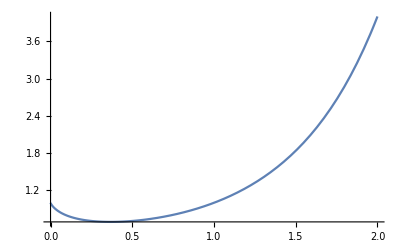

```mathematica
fancyPower[n_] := n^n 
Plot[fancyPower[x], {x, 0, 2}]
```

This says “plot fancyPower as x varies from 0 to 2.” But if we try to plot our bacterial population with this it won’t work. You might try to plot up to generation 10 by writing

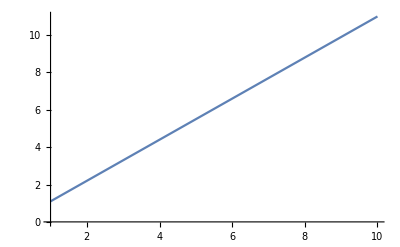

```mathematica
Plot[updatePop[n], {n, 1, 10}]
```

but this only tells how much individuals are in the population given a certain starting population. We can add axis labels to make this clearer.

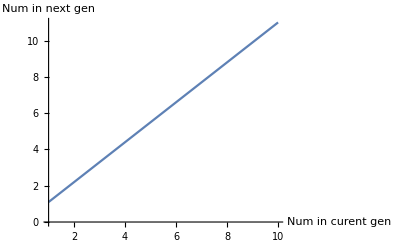

```mathematica
Plot[updatePop[n], {n, 1, 10}, AxesLabel-> {"Num in curent gen", "Num in next gen"}]
```

We want to take the previous generation as input for the next generation, which we cannot do right now. Also this plot would be for continuous values while we want discrete generations (ie. plot not every value between 1 and 10, but just 1, 2, 3, ..., 10). But we can turn the tables with Table.

#### Table

Tables allow us to do things multiple times, and save the entire history of what we did. These are similar to do loops in other programming languages.

```mathematica
Table[2x , {x, -1, 3}]
```

{-2,0,2,4,6}

The output {0,2,4,6,8,10} is a List of values, which is denoted by the curly braces. What this table does is replace x with each value in the list, calculate the answer, and save it. You could perhaps even think of this as a... table.

-Graphics-

You can do multiple lines in the first term of the Table, suppressing the output of each except the last line.

```mathematica
Table[w= x-1;  z = x+1; w*z, {x, 0,5 }]
```

{-1,0,3,8,15,24}

We often will break this up into multiple lines for clarity.  This is the same code to the computer but more readable for the human.

```mathematica
Table[
(* Parameter 1: the code to run and output into the table *)
w= x-1;  (* calculate and supress output *)
z = x+1; (* calculate and supress output *)
w*z, (* calculate and output *)

(* Parameter 2: the range of the x values *)
{x, 0,5 } 
]
```

{-1,0,3,8,15,24}

Now we know enough to make the table of our population growth. Combine variables, functions, and tables to get the following code.

```mathematica
updatePop[n_] := n * 1.1  (* define function *)

currentGeneration = 1618; (* Initial generation *)

data = Table[
(* Calculations *)
currentGeneration = updatePop[currentGeneration]; 
currentGeneration, 

(* From generation 1 to 20 *)
{x, 1, 20}
]
```

{1779.8,1957.78,2153.56,2368.91,2605.81,2866.39,3153.02,3468.33,3815.16,4196.68,4616.34,5077.98,5585.77,6144.35,6758.79,7434.67,8178.13,8995.95,9895.54,10885.1}

We’ve also saved the output in a variable named data. We can now use ListPlot to plot this.

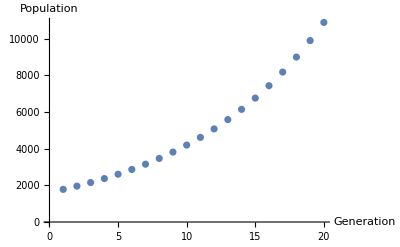

```mathematica
ListPlot[data, AxesLabel-> {"Generation", "Population"}]
```

### Custom x-axis

Maybe instead the population increases by 10% every two hundred generations. We can give each term a custom x term by outputting a list instead of just numbers. Each data point will be of the form {time, population }. The code below is the same as the above except one line has changed.

{{200,1779.8},{400,1957.78},{600,2153.56},{800,2368.91},{1000,2605.81},{1200,2866.39},{1400,3153.02},{1600,3468.33},{1800,3815.16},{2000,4196.68},{2200,4616.34},{2400,5077.98},{2600,5585.77},{2800,6144.35},{3000,6758.79},{3200,7434.67},{3400,8178.13},{3600,8995.95},{3800,9895.54},{4000,10885.1}}

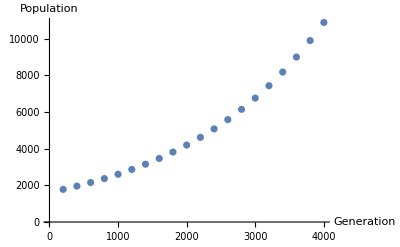

```mathematica
updatePop[n_] := n * 1.1  (* define function *)

currentGeneration = 1618; (* Initial generation *)

data = Table[
(* Calculations *)
currentGeneration = updatePop[currentGeneration]; 
{200x, currentGeneration}, (* 200x will give every two hundred generations *)

(* Time 1 to 20 *)
{x, 1, 20}
]

ListPlot[%, AxesLabel->{"Generation", "Population"}] 
(* Remember that % means the previous thing we calculated, in this case "data". *)
```

#### Getting Fancy

We can compare different growth rates. First make a new update pop function that takes in not only the current population but whatever growth rate we want too. Try writing this function. I’ve filled out the left hand side.

```mathematica
updatePop2[n_, rate_] :=
```

If we wanted to compare five growth rates we would normally have to run the table calculation code five times. That’s a lot to copy paste, and if later we want to change something with the code we would have to change it in five separate places.

This is is a sign that we’d like to put it in a function. Doing so will add clarity to your code and make it easier to change later. For more complicated functions it’s good to add a comment explained how it works. You can encase the left side of a function in parentheses to make longer, more complicated, multiline ones. Any line we do not want to output we put a semicolon on.

```mathematica
(*   Outputs the population graph for generation 1 to numGen starting with a population of initSize growing at rate *)
makePopTable[initSize_, rate_, numGen_  ]:= (
currentGeneration = initSize; (* Initial generation *)

data = Table[
(* Calculations *)
currentGeneration = updatePop2[currentGeneration, rate]; 
currentGeneration, 

(* do this numGen times *)
{x, 1, numGen}
] 
)
```

Now it is easy to see how our population grows for 100 generations.

```mathematica
makePopTable[1618, 1.1, 100]
```

We can now plot this.

```mathematica
ListPlot[makePopTable[1618, 1.1, 100], AxesLabel->{"Generation", "Population"}]
```

Now plot what happens to a population of size 1618 that grows at rate 0.9 for 100 generations.

```mathematica
(* Mimic the code above to make a plot here *)
```

We can plot multiple graphs on the same plot by putting the data in a list.

```mathematica
ListPlot[{makePopTable[1618, .9, 20], makePopTable[1618, 1, 20], makePopTable[1618, 1.1, 20], makePopTable[1618, 1.2, 20]}, AxesLabel->{"Generation", "Population"}, PlotLegends->{"rate = .9", "rate = .1", "rate = 1.1", "rate = 1.2"}]
```

To make it prettier we can make the graphs into line graphs with ListLinePLot.

```mathematica
ListLinePlot[{makePopTable[1618, .9, 20], makePopTable[1618, 1, 20], makePopTable[1618, 1.1, 20], makePopTable[1618, 1.2, 20]}, AxesLabel->{"Generation", "Population"}, PlotLegends->{"rate = .9", "rate = .1", "rate = 1.1", "rate = 1.2"}]
```

Exponential growth appears as a line on a logarithmic plot. Try to figure how to make this a log plot. (Hint: there’s an inbuilt Mathematica function for this. Look it up.) Write the code for the plot in a new cell below.

As written these multiple plots are bad programming style. Say I ask you to change the initial population size to 1000 and the number of generations to 50. Then you'd have to make four changes for each. Rewrite the below code so that the initial population size and the number of generations are both variables. This makes it so to values we only need to change two variables.

```mathematica
(* Rewrite this so 1618 and 20 are replaced with variables. *)
ListLinePlot[{makePopTable[1618, .95, 20], makePopTable[1618, 1, 20], makePopTable[1618, 1.1, 20], makePopTable[1618, 1.2, 20]}, AxesLabel->{"Generation", "Population"}, PlotLegends->{"rate = .95", "rate = .1", "rate = 1.1", "rate = 1.2"}]
```

Now play around, changing the initial population and generation number to see what happens.

## 5. Recursive Functions (aka Recurrence Equations)

Functions can reference themselves. This gives us an alternative way to simulate our population. Just notice that the population at some time t is the same as the population at time t-1 times whatever it’s growth rate is. If the growth rate is 1.1 then we can write

```mathematica
(* Set up the recurrence function *)
pop[t_] := pop[t-1] 1.1  ;
pop[1] = 1618;
```

Then to calculate the size of generation 100 we just type

```mathematica
pop[100]
```

2.027×10^7

And to get the table and plots we write

```mathematica
(* Table of 20 generations *)
Table[pop[t], {t, 1, 20}]
```

{1618,1779.8,1957.78,2153.56,2368.91,2605.81,2866.39,3153.02,3468.33,3815.16,4196.68,4616.34,5077.98,5585.77,6144.35,6758.79,7434.67,8178.13,8995.95,9895.54}

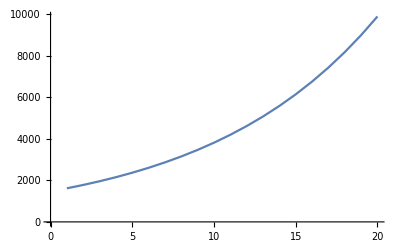

```mathematica
(* Plot the table we just calculated *)
ListLinePlot[%]
```

The pop[1] = 1618 line sets the initial conditions.  It tells Mathematica to treat pop[1] as a variable equal to 1618. Otherwise we would have an infinite regress where Mathematica keeps looking for the previous time and never stops.

-Graphics-

Well, Mathematica will eventually stop and throw you a recurrence error.

```mathematica
turtle[n_] := "turtle" + turtle[n-1];
```

```mathematica
turtle[12]
```

If you see an error like 

-Graphics-
It usually means you have infinite loop hanging around. Try fixing the turtle function by adding an initial condition. Remember to use equals, not colon-equals.

Another infinite recursion is shown below. This is because the function loops back to itself and never gets to the initial condition.

```mathematica
g[s_] := g[s] 
g[1] = 46290

g[5]
```

If you try to plot a function that has an error then you’ll get a blank plot back.

```mathematica
Plot[g[x], {x, 0, 10}]
```

-Graphics-

## 6. Analytic Solutions

Programming is advanced laziness. Instead of having to, by hand, calculate out how a population grows for a thousand generations we have written a function which does it in two lines. We’re working smart, not hard.

```mathematica
pop[t_] := pop[t-1] 1.1  ;
pop[1] = 1618;
```

```mathematica
ListLinePlot[Table[pop[t], {t, 1, 1000}] ]
```

-Graphics-

But we can be even smarter with a little mathematical reasoning. This is what is known in the field as being big-brain. Think of population growth in terms of our recurrence equation.

-Graphics-

(Note: In this class we’ll be switching between mathematical notation and Mathematica notation a lot. In mathematics a function is denoted like f(x) while in Mathematica it is f[x]. Also equals, in the sense of “is the same as”, is simply = in math but is == in Mathematica. You’ll have to turn to context to figure out which notation we are using.)

Substitute pop(n-2)1.1 in for the pop(n-1) term in the above equation. Keep doing this until you get to you initial condition. For example, if we started with n = 4. 

-Graphics-

We just took the initial population and multipled it by the growth rate for each new generation. Generalizing this for any growth rate r we can find a simple formula. 

-Graphics-

Thus the big-brain way to find the population size at generation 100, for a population with initial size 1618 and growth rate 1.1, is

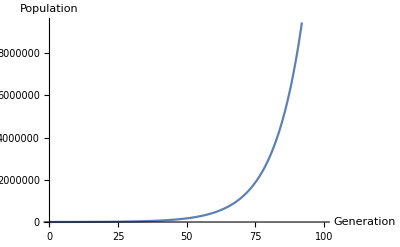

```mathematica
cleverPop[t_] := 1618 (1.1)^(t-1)
Plot[cleverPop[t], {t, 0, 100}, AxesLabel->{"Generation", "Population"}]
```

We can define a version that takes in the growth rate and initial population

```mathematica
cleverPop[t_, r_, init_] := init r^(t-1)
```

Now plot three graphs for tmax generations for varying values of r.

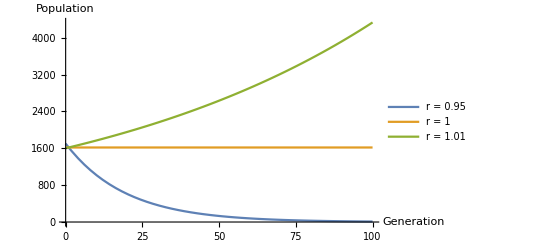

```mathematica
tmax = 100;
initialPop = 1618;

Plot[
{cleverPop[t,.95,initialPop], 
cleverPop[t,1,initialPop],
cleverPop[t,1.01,initialPop]},

{t, 0, tmax},
 AxesLabel->{"Generation", "Population"},
PlotLegends->{"r = 0.95", "r = 1", "r = 1.01"}]
```

The grail of mathematical biology is to find these “analytic solutions.” These are equations that describe the system perfectly. With them we don’t even have to simulate; we just plug numbers into an equation and it lets us perfectly predict what happens.

Usually we can only find analytical solutions to the simplest systems. You can often mathematically prove that for more advanced systems it is impossible to find an analytic solution. Same is often true for when we introduce randomness into the system. In those cases it’s often easier to work with tables, which we do in the randomness section later.

#### Functions with multiple inputs.

Notice from the above that it’s totally okay to define different versions of functions for different number of inputs.

```mathematica
f[] := 1
f[n_] := n^2
f[n_, m_ ] := (n+m)^(2m)
```

```mathematica
f[]
f[2]
f[2,1]
```

1

4

9

## 7. The magic of manipulation

With the Manipulate function we can take these graphs and bend them to our will make them interactive.

```mathematica
cleverPop[t_] := 1618 (1.1)^(t-1)
cleverPop[t_, r_, init_] := init r^(t-1)
```

```mathematica
Manipulate[cleverPop[t], {t,0,10}]
```

We can manipulate anything.

```mathematica
Manipulate[
(* What we're manipulating *)
Plot[cleverPop[t,r,1618],{t, 0, 10},
 AxesLabel->{"Generation", "Population"}],

(* Sliders that we manipulate and their ranges *)
{r, 0.0001, 5}]
```

We can manipulate multiple parameters too.

```mathematica
Manipulate[

(* What we're manipulating *)
Plot[cleverPop[t,r,init],{t, 0, tmax},
 AxesLabel->{"Generation", "Population"}],

(* Sliders that we manipulate and their ranges *)
{r, 0.0001, 5},
{tmax, 5, 50},
{init, 1,100}]
```

We put the minimum value of r at a very low number instead of 0. This is because if we set it to zero then in our calculations we divide by zero. If you do this in Manipulate Mathematica gets angry and spits multiple errors at you. It might also crash and delete all your unsaved work out of spite.

```mathematica
1/0
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

## 8. Randomness and Multiple Function Inputs

#### Random Functions

Often the environment might vary generation to generation and so give us random growth rates. Mathematica has a whole suite of random number generating functions to help with this. Each time you re-run a random function it will give you a new random number.

RandomReal spits out a random number between 0 and 1.

```mathematica
RandomReal[]
```

0.473118

```mathematica
RandomReal[{41, 43}]
```

42.8957

RandomInteger is like RandomReal but more old school because it’s just with integers.

```mathematica
RandomInteger[{1,10}]
```

9

You can add a second number at the end to chose multiple random integers.

```mathematica
RandomInteger[{1,10}, 5] (* Choose 5 random integers between 1 and 10 *)
```

{7,5,10,8,9}

RandomChoice uses a set of probabilities to make a random choice

```mathematica
RandomChoice[{"eat","sleep","mate", "Netflix"}]
```

mate

You can give each of these certain probabilities.

```mathematica
RandomChoice[{.1,.2, 0,.7}->{"eat","sleep","mate", "Netflix"}]
```

Netflix

Choose elements from a list without replacement. The list could be anything!

```mathematica
RandomSample[{abba,666,"hello",-E^(Pi I),{"this is a list in a list", "listception"}, -Graphics-},3]
```

{hello,abba,-Graphics-}

#### Random Growth Rates

Say that sometimes the environment is nice and the bacteria grow fast and sometimes the environment is literally on fire and their growth rate slows. Say when it is good the rate is 1.1 and when it is bad it is .95. (These are fairly fire resistant bacteria.) Each environment happens half of the time.

Modify our previous code to output this new growth.

```mathematica
(* Hint: replace the growth rate term *)
cleverPop[t_] := cleverPop[t-1] 1.1
cleverPop[1] = 1618;

Table[cleverPop[t], {t, 1, 100}];
ListLinePlot[%, AxesLabel->{"Generation", "Population"}]
```

If you did this right you should get a graph that looks something like. It’ll be different each time you run it.

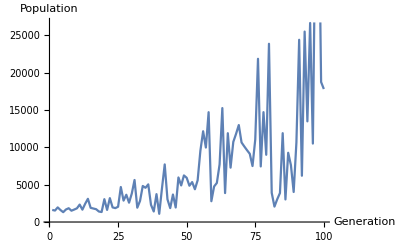

## 9. Summary

-Graphics-

## 10. Bonus Tips and Tricks

Here’s are some bonus tips and tricks, not in any particular order.

List of Hotkeys: https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html
How to enable autosave: https://support.wolfram.com/25948

#### Rounding

Mathematica likes to keep things exact for as long as possible. It might simplify, but it’ll keep things exact.

```mathematica
(π  3)^2
```

If you want the decimal value you can use the N function.

```mathematica
(π  3)^2 // N
```

(Remember double slash also applies a function.) You could also write one of the numbers as a decimal and it’ll do it automatically.

```mathematica
(π  3.0)^2
```

#### Things not plotting

Functions will not plot if it still has some undefined terms in it, or anything that isn’t a number. Mathematica needs to calculate something to a number to plot it.

```mathematica
coolFunction[x_] := m x + b
Plot[coolFunction[x], {x, 0, 10}]
```

-Graphics-

You can see that it does not evaluate to a number if you ask it what the value of the function is at a certain number.

```mathematica
coolFunction[4]
```

If we fix that by setting b and m to be numbers then all is good.

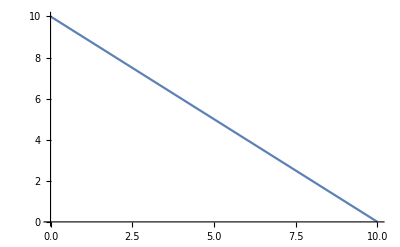

```mathematica
b= 10;
m = -1;
Plot[coolFunction[x], {x, 0, 10}]
```

Another reason things might not plot is if they are imaginary or complex numbers. These won’t come up much in this class but will in more advanced modeling.

```mathematica
euler[x_] := E^(I Pi x)
```

This function is imaginary for non-integer values of x.

```mathematica
Manipulate[
euler[x],
{x,0,10}]
```

Plots will only show the real numbers. If only a few points are real Mathmatica might not even display them.

```mathematica
Plot[euler[x], {x, 0, 10}]
```

-Graphics-

If you suspect this is happening try to only plot the real part.

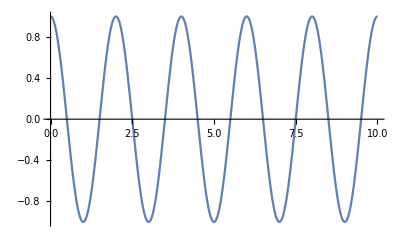

```mathematica
Plot[Re[euler[x]], {x, 0, 10}]
```

#### Mapping Functions

Maybe we have a list of numbers. Pretend these are the successive population sizes of organisms over a hundred generations which just so happen to be the first hundred prime numbers.

```mathematica
primes = Table[Prime[n], {n, 1, 100}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

We want to take the logarithm of each of these.  We can do this with the map function. The notation /@ applies the function to every entry in the list.

```mathematica
Log /@ primes
```

{Log[2],Log[3],Log[5],Log[7],Log[11],Log[13],Log[17],Log[19],Log[23],Log[29],Log[31],Log[37],Log[41],Log[43],Log[47],Log[53],Log[59],Log[61],Log[67],Log[71],Log[73],Log[79],Log[83],Log[89],Log[97],Log[101],Log[103],Log[107],Log[109],Log[113],Log[127],Log[131],Log[137],Log[139],Log[149],Log[151],Log[157],Log[163],Log[167],Log[173],Log[179],Log[181],Log[191],Log[193],Log[197],Log[199],Log[211],Log[223],Log[227],Log[229],Log[233],Log[239],Log[241],Log[251],Log[257],Log[263],Log[269],Log[271],Log[277],Log[281],Log[283],Log[293],Log[307],Log[311],Log[313],Log[317],Log[331],Log[337],Log[347],Log[349],Log[353],Log[359],Log[367],Log[373],Log[379],Log[383],Log[389],Log[397],Log[401],Log[409],Log[419],Log[421],Log[431],Log[433],Log[439],Log[443],Log[449],Log[457],Log[461],Log[463],Log[467],Log[479],Log[487],Log[491],Log[499],Log[503],Log[509],Log[521],Log[523],Log[541]}

Mathematica is trying to stay exact so we can apply the N function to make these decimals.

```mathematica
Log /@ primes  // N
```

{0.693147,1.09861,1.60944,1.94591,2.3979,2.56495,2.83321,2.94444,3.13549,3.3673,3.43399,3.61092,3.71357,3.7612,3.85015,3.97029,4.07754,4.11087,4.20469,4.26268,4.29046,4.36945,4.41884,4.48864,4.57471,4.61512,4.63473,4.67283,4.69135,4.72739,4.84419,4.8752,4.91998,4.93447,5.00395,5.01728,5.05625,5.09375,5.11799,5.15329,5.18739,5.1985,5.25227,5.26269,5.2832,5.2933,5.35186,5.40717,5.42495,5.43372,5.45104,5.47646,5.4848,5.52545,5.54908,5.57215,5.59471,5.60212,5.62402,5.63835,5.64545,5.68017,5.72685,5.73979,5.7462,5.7589,5.80212,5.82008,5.84932,5.85507,5.86647,5.88332,5.90536,5.92158,5.93754,5.94803,5.96358,5.98394,5.99396,6.01372,6.03787,6.04263,6.06611,6.07074,6.0845,6.09357,6.10702,6.12468,6.1334,6.13773,6.14633,6.1717,6.18826,6.19644,6.21261,6.22059,6.23245,6.25575,6.25958,6.29342}

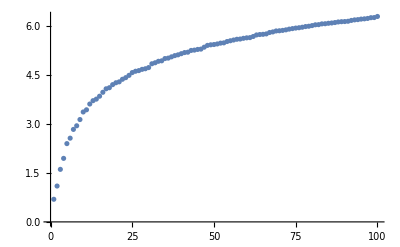

```mathematica
ListPlot[Log /@ primes]
```

Say that you hear that, when divided by four, there are consistently more primes with remainder 3 then with remainder 1. (At least for a while.) This sounds suspect to you so you want to check this on the first hundred primes. You happen to know that the Mod function gives the remainder after dividing by four.

```mathematica
?Mod
```

Mod[m,n] gives the remainder on division of m by n. 
Mod[m,n,d] uses an offset d.

```mathematica
Mod[7,4]
```

3

We can apply the primes to the first term of Mod with this following notation.

{2,3,1,3,3,1,1,3,3,1,3,1,1,3,3,1,3,1,3,3,1,3,3,1,1,1,3,3,1,1,3,3,1,3,1,3,1,3,3,1,3,1,3,1,1,3,3,3,3,1,1,3,1,3,1,3,1,3,1,1,3,1,3,3,1,1,3,1,3,1,1,3,3,1,3,3,1,1,1,1,3,1,3,1,3,3,1,1,1,3,3,3,3,3,3,3,1,1,3,1}

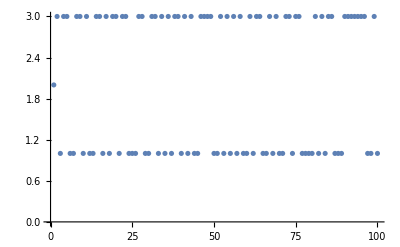

```mathematica
r = Mod[#,4] &/@ primes 
ListPlot[r]
```

Counting the values we see that remainder 3 is indeed greater when we have 100 primes.

```mathematica
Count[r, 1]
Count[r, 3]
```

47

52

But what about for other number of primes? Automating and plotting this we can make a graph.

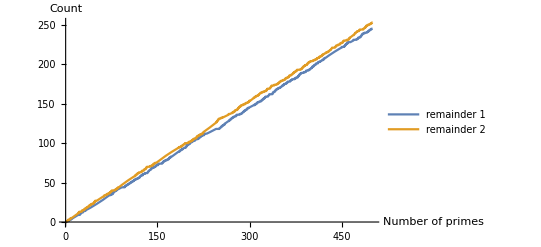

```mathematica
res[n_] := Mod[#,4] &/@ Table[Prime[x], {x, 1, n}];
Plot[{Count[res[n],1], Count[res[n],3]}, {n, 1, 500}, PlotLegends->{"remainder 1", "remainder 2"}, AxesLabel->{"Number of primes","Count"}]
```

#### Multiple % signs.

Multiple % signs take you further back in the past.

```mathematica
1+1;
1+2;
2+3;
{%, %%, %%%}
```

{5,3,2}

#### Matrices

Lists of lists correspond to matrices in Mathematica

```mathematica
m = {{1, 1},{1,0}};
m // MatrixForm (* MatrixForm just displays it to look like a matrix *)
```

(1 | 1
1 | 0)

Matrix multiplication is done with the dot operation

```mathematica
m.m // MatrixForm
```

(2 | 1
1 | 1)

You can do more advanced matrix algebra. We probably won’t do too much in this class, but this section is here for those that might in the future.

```mathematica
(* Matrix times a scalar *)
```

```mathematica
3m // MatrixForm
```

(3 | 3
3 | 0)

```mathematica
(* Matrix times a vector *)
```

```mathematica
m.{2,2} // MatrixForm
```

(4
2)

```mathematica
(* Powers of a matrix *)
```

```mathematica
Table[MatrixPower[m, t] // MatrixForm, {t, 1,10}]
```

{(1 | 1
1 | 0),(2 | 1
1 | 1),(3 | 2
2 | 1),(5 | 3
3 | 2),(8 | 5
5 | 3),(13 | 8
8 | 5),(21 | 13
13 | 8),(34 | 21
21 | 13),(55 | 34
34 | 21),(89 | 55
55 | 34)}

```mathematica
(* Eigenvectors and Eigenvalues *)
Eigenvalues[m]
MatrixForm /@ Eigenvectors[m]
```

{1/2 (1+√5),1/2 (1-√5)}

{(1/2 (1+√5)
1),(1/2 (1-√5)
1)}

#### 3D Plots

Here’s our original analytic solution

```mathematica
cleverPop[t_, r_, init_] := init r^(t-1)

Manipulate[

(* What we're manipulating *)
Plot[cleverPop[t,r,initpop],{t, 0, tmax},
 AxesLabel->{"Generation", "Population"}],

(* Sliders that we manipulate and their ranges *)
{r, 0.0001, 5},
{tmax, 5, 500},
{initpop, 1, 1000} ]
```

This is nice, but we are only visualizing the generation and populations right now. We live in three dimensions so we could add one more axis to this graph. Say we add r. This lets is visualize all the growth rates at once.

```mathematica
?Plot3D
```

```mathematica
Manipulate[
Plot3D[cleverPop[t, r, initPop], {t, 0, tmax}, {r, 0.01, 5}, AxesLabel->{"Generation", "r","Population"}],

{tmax, 5, 50},
{initPop, 1, 1000}
]
```

Our line plot is just slices of this plot as we vary r.